```mathematica
Needs["PlotLegends`"]
```

```mathematica
nmax = 10;
α = 0.6;
c = 2.997 10^8;hbar = 1.0545718×10^-34;
λ = 455.527 10^-9 ;
ω = c 2 Pi/λ;
λLat = 532 10^-9;
Γ = 1.84 10^6;
ωLat = c * 2 Pi / (λLat);
IntensityLat = 1 /(10^-4);(*from other simulation*)
kb = 1.38066 10^-23;
ω0 = 1.3 10^6;
Ωfree = 2 Pi 30.6 10^3;
ΩRm1 = Sqrt[2 Pi 30.6 10^3];
ΩRm2 = Sqrt[2 Pi 30.6 10^3];
ΔRm = 10^9;
ΔR = 10^12;
(*lattice params*)
a = 532 10^-9;
σ = 0.1 *3 * (265 10^-12)^2/(2 Pi);
ρ = 1/a^2;
RCs = 500;
Dr[n_,nt_]:= √((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η 1)^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η 1)^2]Exp[-η^2/2];
```

```mathematica
Calculation of Scattering Rates Γeff(n)
```

```mathematica
Clear[P1list,P2list];
P1list = {};
P2list = {};
P3list = {};
tab = Table[
(*alpha factor to be guessed /measured*)
δ1 = 1;
δ2 = 1;
η = 0.2;
Ω1 = 50 2 Pi 10^3;
Ωn = Ω1 Sqrt[n];(*(√((n!)/((n+n-1-n)!))(ⅈ η 1)^(n-1-n)LaguerreL[n,n-1-n,(η 1)^2]*Exp[-η^2/2])^2;*)
Int = 0.6 10^-3/(10^-4);
h = 2 Pi *hbar;
;ΩR = Sqrt[(3 λ^3 Γ Int)/(2 Pi h c)];

H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ΩR}, {0, ΩR, -2 δ2}});
If[n == 0, α=1, dummy = 0]
Γ1 = α η^2 (n+1) Γ;
Γ2 = (1-α)(1-η^2(2n - 1))Γ;
Γo = Γ - Γ1 - Γ2;

L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}});
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
dρdt =(-ⅈ/hbar(H. ρe[t]- ρe[t]. H)+L);
ρen= Flatten[({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}})];
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]];
init={ρ11[0] == 1, ρ12[0] == 0,ρ13[0] == 0,ρ21[0] == 0,ρ22[0] == 0,ρ23[0] == 0,ρ31[0] == 0,ρ32[0] == 0,ρ33[0] == 0};
sol=NDSolve[Join[system&&init],ρen,{t,0,10*10^-1}, MaxSteps-> 100000];
fun3=ρ33/.First[sol];
fun1=ρ11/.First[sol];
fun2 = ρ22 /. First[sol];
expsol = Solve[Re[fun3[4 10^-5  ]] == Re[fun3[1 10^-5 ]] Exp[-l 3 10^-5 ],l];
la = l /. expsol;
If[n==0, lam = 0, lam = First[la] Γ/Γo];
AppendTo[P1list, Re[fun1[1 10^-5 ]] /(Re[fun1[1 10^-5 ]] +Re[fun2[1 10^-5 ]] +Re[fun3[1 10^-5 ]]  )];
AppendTo[P2list, Re[fun2[1 10^-5 ]] /(Re[fun1[1 10^-5 ]] +Re[fun2[1 10^-5 ]] +Re[fun3[1 10^-5 ]]  )];
AppendTo[P3list, Re[fun3[1 10^-5 ]] /(Re[fun1[1 10^-5 ]] +Re[fun2[1 10^-5 ]] +Re[fun3[1 10^-5 ]]  )];
{n,lam},{n,0,10}]
Γscatt = tab[[All, 2]]
P1list
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

{{0,0},{1,71289.},{2,141868.},{3,208622.},{4,269385.},{5,321625.},{6,362704.},{7,391025.},{8,407470.},{9,414540.},{10,415504.}}

{0,71289.,141868.,208622.,269385.,321625.,362704.,391025.,407470.,414540.,415504.}

{1.,0.913446,0.834965,0.762834,0.695124,0.633053,0.580301,0.538549,0.505567,0.47784,0.453576}

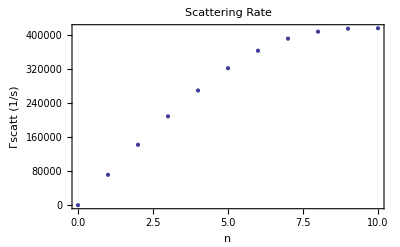

```mathematica
ListPlot[tab, FrameLabel-> {"n","Γscatt (1/s)"}, PlotLabel-> "Scattering Rate", Frame-> True]
```

```mathematica
(Plots: Scattering Rate As a Function of Raman and Repump Coupling strengths.)
```

```mathematica
tabrepump =Table[ Table[
(*alpha factor to be guessed /measured*)
α = 0.6;
Γ = 1.84 10^6;
Ωfree = 2 Pi 30.6 10^3;
δ1 = 1;
δ2 = 1;
η = 0.2;
Ω1 = 50 2 Pi 10^3;
Ωn = Ω1 Sqrt[n];(*(√((n!)/((n+n-1-n)!))(ⅈ η 1)^(n-1-n)LaguerreL[n,n-1-n,(η 1)^2]*Exp[-η^2/2])^2;*)
hbar = 1.0545718×10^-34;
λ = 455.527 10^-9 ;
Int = 0.9 10^-3/(10^-4);
h = 2 Pi *hbar;
c = 2.997 10^8;
(*ΩR = Sqrt[(3 λ^3 Γ Int)/(2 Pi h c)];*)
H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ΩR}, {0, ΩR, -2 δ2}});
If[n == 0, α=1, dummy = 0]
Γ1 = α η^2 (n+1) Γ;
Γ2 = (1-α)(1-η^2(2n - 1))Γ;
Γo = Γ - Γ1 - Γ2;

L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}});
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
dρdt =(-ⅈ/hbar(H. ρe[t]- ρe[t]. H)+L);
ρen= Flatten[({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}})];
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]];
init={ρ11[0] == 1, ρ12[0] == 0,ρ13[0] == 0,ρ21[0] == 0,ρ22[0] == 0,ρ23[0] == 0,ρ31[0] == 0,ρ32[0] == 0,ρ33[0] == 0};
sol=NDSolve[Join[system&&init],ρen,{t,0,10*10^-5}, MaxSteps-> 1000000];
fun=ρ33/.First[sol];
expsol = Solve[Re[fun[8 10^-5  ]] == Re[fun[5 10^-5 ]] Exp[-l  3 10^-5 ],l];
la = l /. expsol;
If[n==0, lam = 0, lam = First[la] Γ/Γo];
{ΩR,lam},{ΩR,0,4 10^6, 0.5 10^5}],{n,0,10}];
```

Set::write: Tag Times in 0\ 485760. is Protected.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Set::write: Tag Times in 0\ 485760. is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

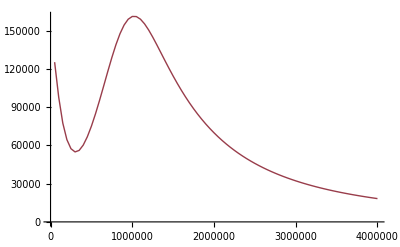
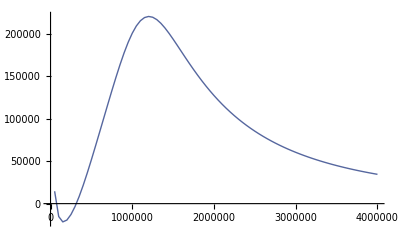
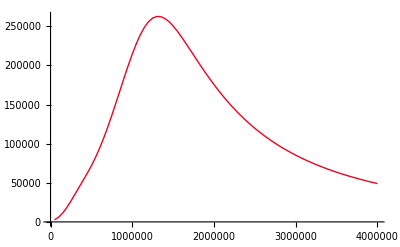
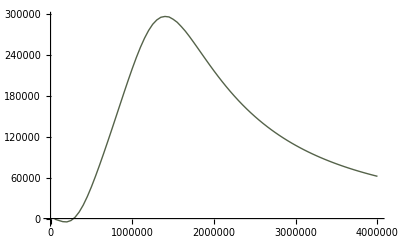
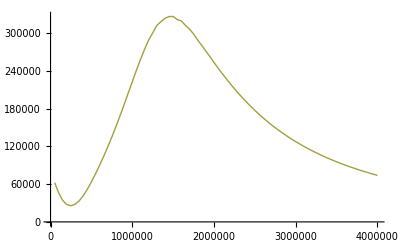
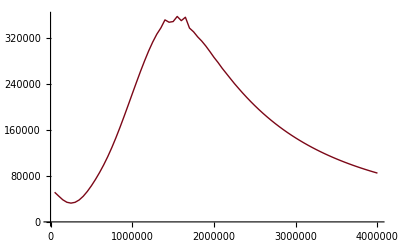
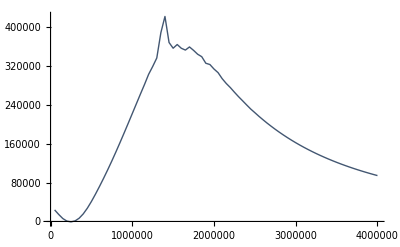
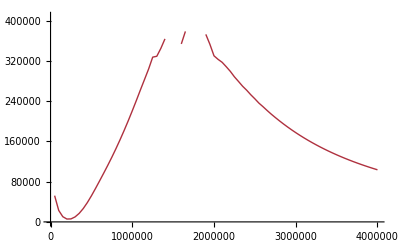

```mathematica
repumplots = Table[ListLinePlot[tabrepump[[n]], PlotStyle-> ColorData[n,"ColorList"]],{n,1,10}]
```

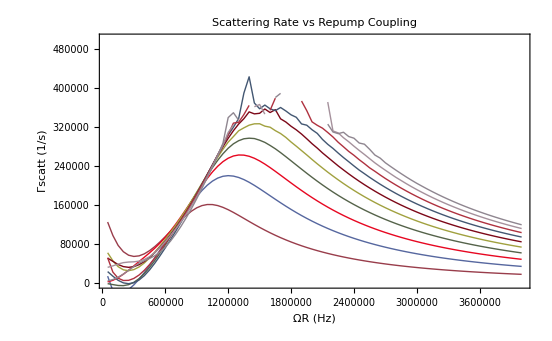

```mathematica
Show[repumplots , PlotRange -> {All,{0,500000}}, FrameLabel-> {"ΩR (Hz)","Γscatt (1/s)"}, PlotLabel-> "Scattering Rate vs Repump Coupling", Frame-> True]
```

```mathematica
tabraman=Table[ Table[
(*alpha factor to be guessed /measured*)
α = 0.6;
Γ = 1.84 10^6;
Ωfree = 2 Pi 30.6 10^3;
δ1 = 1;
δ2 = 1;
η = 0.2;
(*Ω1 = 50 2 Pi 10^3;*)
Ωn = Ω1 Sqrt[n];(*(√((n!)/((n+n-1-n)!))(ⅈ η 1)^(n-1-n)LaguerreL[n,n-1-n,(η 1)^2]*Exp[-η^2/2])^2;*)
hbar = 1.0545718×10^-34;
λ = 455.527 10^-9 ;
Int = 0.9 10^-3/(10^-4);
h = 2 Pi *hbar;
c = 2.997 10^8;
ΩR = Sqrt[(3 λ^3 Γ Int)/(2 Pi h c)];
H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ΩR}, {0, ΩR, -2 δ2}});
If[n == 0, α=1, dummy = 0]
Γ1 = α η^2 (n+1) Γ;
Γ2 = (1-α)(1-η^2(2n - 1))Γ;
Γo = Γ - Γ1 - Γ2;

L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}});
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
dρdt =(-ⅈ/hbar(H. ρe[t]- ρe[t]. H)+L);
ρen= Flatten[({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}})];
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]];
init={ρ11[0] == 1, ρ12[0] == 0,ρ13[0] == 0,ρ21[0] == 0,ρ22[0] == 0,ρ23[0] == 0,ρ31[0] == 0,ρ32[0] == 0,ρ33[0] == 0};
sol=NDSolve[Join[system&&init],ρen,{t,0,10*10^-1}, MaxSteps-> 100000];
fun=ρ33/.First[sol];
expsol = Solve[Re[fun[10 10^-5  ]] == Re[fun[3 10^-5 ]] Exp[-l  7 10^-5 ],l];
la = l /. expsol;
If[n==0, lam = 0, lam = First[la] Γ/Γo];
{Ω1,lam},{Ω1,0,2.5 10^6, 2 10^4}],{n,0,10}];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.00730591.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.00719219.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.00706502.

General::stop: Further output of NDSolve :: mxst will be suppressed during this calculation.

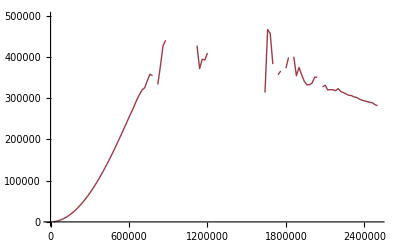
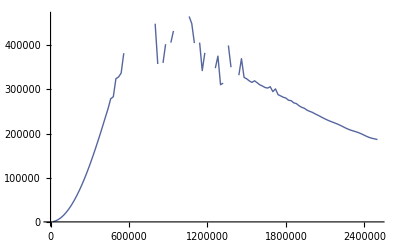
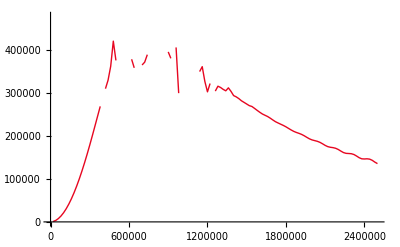
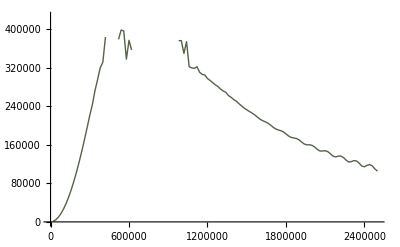
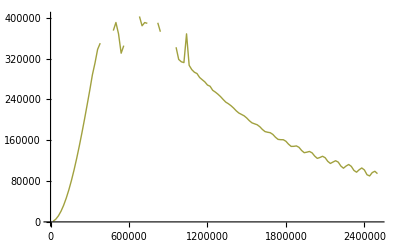
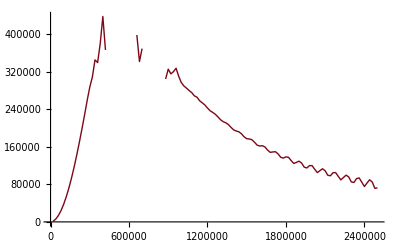
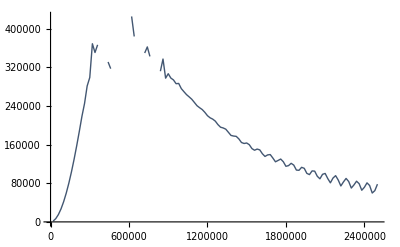
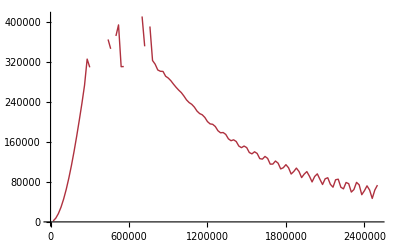

```mathematica
ramanplots = Table[ListLinePlot[tabraman[[n]], PlotStyle-> ColorData[n,"ColorList"]],{n,1,10}]
```

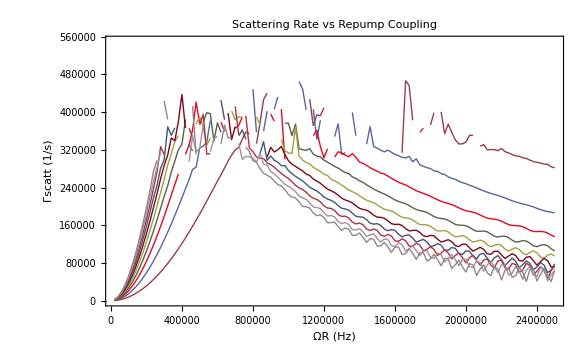

```mathematica
Show[ramanplots , PlotRange -> {All,{0,550000}}, FrameLabel-> {"ΩR (Hz)","Γscatt (1/s)"}, PlotLabel-> "Scattering Rate vs Repump Coupling", Frame-> True]
```

```mathematica
Photon recoil
```

```mathematica
Γscatt;
pphoton = h / λ;
mCs = 132.90545 * 1.660539 10^-27 ;(*internet*)
Erecoil = pphoton^2/(2mCs);

Λreca= Γscatt * Erecoil;
Λrece= Γscatt * Erecoil;
Λrecarate= Γscatt * Erecoil    2/(3 kb) *10^3;
Λrecerate= Γscatt * Erecoil    2/(3 kb) *10^3
```

{0.,16.5009,32.8374,48.2884,62.3531,74.4447,83.9529,90.5082,94.3148,95.9513,96.1743}

```mathematica
Off-resonant scattering: Raman
```

```mathematica
Ephoton = h * c/λ;
ΛscRm =Table[ Γ    (ΩRm1^2 + ΩRm2^2)/(4 ΔRm^2) Ephoton ,{n,0,10}] 2/(3 kb)10^3
```

{3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234}

```mathematica
Off-resonant scattering: Repump beam
```

```mathematica
ΛscRp = P1list* Γ ΩR^2/(4 ΔR^2)Ephoton 2/(3 kb)10^3
```

{24.2951,22.1923,20.2856,18.5331,16.8881,15.3801,14.0985,13.0841,12.2828,11.6092,11.0197}

```mathematica
Lattice beams
```

```mathematica
(*ephoton not precise, should be average over all resonances*)
(*numerical value taken from last weeks simulartion*)
```

```mathematica
ΛscLat =  Table[1.00217872738179 10^-9 * IntensityLat 2*hbar ω 2/(3 kb) *10^3 ,{n,0,10}]
```

{421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916}

```mathematica
Off-Res Raman Couplings: Carrier transitions n-> n
```

```mathematica
Ωcarrier = Table[Ω1 (1-0.5 η^2(2n+1)),{n,0,10}];
```

```mathematica
Λcarrier = Table[P1list[[n+1]] ΩR^2/Γ Ωcarrier[[n+1]]^2/(4 ω0^2),{n,0,10}]2*Erecoil 2/(3 kb) *10^3
```

{8.85139,6.83716,5.38848,4.32944,3.51463,2.87118,2.37361,2.00075,1.71738,1.48126,1.25962}

```mathematica
Off-Res Raman Couplings: Blue transitions
```

```mathematica
Ωblue = Table[Ω1 (Sqrt[n+1]),{n,0,10}]//N;
```

```mathematica
Λblue= Table[P1list[[n+1]] ΩR^2/Γ Ωblue[[n+1]]^2/(16 ω0^2),{n,0,10}]hbar ω0 2/(3 kb) *10^3
```

{32.9478,60.1922,82.5309,100.535,114.514,125.146,133.838,141.952,149.916,157.438,164.388}

```mathematica
Off-Res Raman Couplings: Doubly red
```

```mathematica
Ωdoublyred= Table[Ωcarrier[[1]]*η^2*Sqrt[(n-1)*n],{n,0,10}]//N;
```

```mathematica
Λdoublyred = -Table[P1list[[n+1]] ΩR^2/Γ Ωdoublyred[[n+1]]^2/(4 ω0^2),{n,0,10}]hbar ω0 2/(3 kb) *10^3
```

{0.,0.,-0.268976,-0.710051,-1.26805,-1.90811,-2.62887,-3.46696,-4.46345,-5.60898,-6.81286}

```mathematica
Rescattering
```

```mathematica
Λresc = Table[(P1list[[n+1]]α+P2list[[n+1]](1-α)) 1.00217872738179 10^9 (σ ρ)/2 Log[RCs],{n,0,10}]*2/(3 kb) *10^3 *2* Erecoil
```

{0.0170786,0.0156004,0.01426,0.0130282,0.0118718,0.0108117,0.00991074,0.00919768,0.00863438,0.00816085,0.00774645}

```mathematica
Repumping of state 2
```

```mathematica
Γ2s = ΩR^2 Γ/(Γ^2+4 δ2^2);
ΛRepump = Table[P2list[[n+1]] * Γ2s *2* Erecoil,{n,0,10}] 2/(3 kb) *10^3
```

{0.,63.7699,109.833,143.748,170.02,190.053,203.614,211.331,215.754,220.592,228.846}

```mathematica
Cooling Rate
```

```mathematica
Λcool = -Table[P3list[[n+1]] α Abs[Dr[n-1,n-1]]^2*Γ,{n,0,10}] 2/(3 kb) *10^3 hbar ω0;
Λcool[[1]] = 0;
Λcool
```

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

{0,-417.095,-674.299,-816.413,-893.988,-936.409,-949.29,-929.301,-877.511,-803.885,-724.212}

```mathematica
Generate table
```

```mathematica
TableOfValues2=MapThread[Prepend,{{{"n = 0","n=1","n=2","n=3","n=4","n=5","n=6","n=7","n=8","n=9","n=10"},Λrecarate, Λrecerate,Λcarrier ,Λblue  ,ΛscRm ,ΛscRp ,Λresc,ΛscLat, Λdoublyred,Λcool},{"μK/ms","Λrecarate", "Λrecerate","Λcarrier" ,"Λblue"  ,"ΛscRm" ,"ΛscRp" ,"Λresc","ΛscLat","Λdoublyred","Λcool"}}];
Grid[TableOfValues2[[All,{1,2,3,6,8,10,12}]],ItemStyle->{Automatic,{1->{Bold,14}}},Frame->{All,1->True},Background->{None,{{LightOrange,LightGray}}}]
```

μK/ms | n = 0 | n=1 | n=4 | n=6 | n=8 | n=10
Λrecarate | 0. | 16.5009 | 62.3531 | 83.9529 | 94.3148 | 96.1743
Λrecerate | 0. | 16.5009 | 62.3531 | 83.9529 | 94.3148 | 96.1743
Λcarrier | 8.85139 | 6.83716 | 3.51463 | 2.37361 | 1.71738 | 1.25962
Λblue | 32.9478 | 60.1922 | 114.514 | 133.838 | 149.916 | 164.388
ΛscRm | 3.7234 | 3.7234 | 3.7234 | 3.7234 | 3.7234 | 3.7234
ΛscRp | 24.2951 | 22.1923 | 16.8881 | 14.0985 | 12.2828 | 11.0197
Λresc | 0.0170786 | 0.0156004 | 0.0118718 | 0.00991074 | 0.00863438 | 0.00774645
ΛscLat | 421.916 | 421.916 | 421.916 | 421.916 | 421.916 | 421.916
Λdoublyred | 0. | 0. | -1.26805 | -2.62887 | -4.46345 | -6.81286
Λcool | 0 | -417.095 | -893.988 | -949.29 | -877.511 | -724.212

```mathematica
Rate equation
```

```mathematica
Matrix Elements (from seperate notebook)
```

```mathematica
Matd ={{0.0005005757396031552,0.011549647191876785+0. ⅈ,0.0010654538240816782,0.00005696707197169416+0. ⅈ,2.138143791575166*^-6,6.189500572242522*^-8+0. ⅈ,1.4713483387961095*^-9,2.99231166794164*^-11+0. ⅈ,5.348622136781113*^-13,8.5583070619037*^-15+0. ⅈ,1.242051750621358*^-16},{0.03697553462304422+0. ⅈ,0.8542748578182446,0.08900855228087623+0. ⅈ,0.006385606547445294,0.0003245377723380953+0. ⅈ,0.00001264438819162315,3.9808740080362333*^-7+0. ⅈ,1.049976520641568*^-8,2.3811020858372025*^-10+0. ⅈ,4.734016075422367*^-12,8.37794464301729*^-14+0. ⅈ},{0.0016586656982055252,0.08903630877416517+0. ⅈ,0.7765460264171041,0.12005099030576624+0. ⅈ,0.011755486055422308,0.0007597207173820889+0. ⅈ,0.00003593126887562029,1.3304500930880276*^-6+0. ⅈ,4.034240729030686*^-8,1.0339001162413906*^-9+0. ⅈ,2.2926703445707534*^-11},{0.00007326736875717263+0. ⅈ,0.00637046190261678,0.1200586112360612+0. ⅈ,0.7083822048191791,0.14546706493155676+0. ⅈ,0.018137407132661792,0.001426490368235323+0. ⅈ,0.00007950593599214194,3.3894529693598402*^-6+0. ⅈ,1.1627272868742031*^-7,3.3271717909823495*^-9+0. ⅈ},{2.4493286500748285*^-6,0.00032410219918417295+0. ⅈ,0.011755694931406884,0.14546707187603547+0. ⅈ,0.6495044336655601,0.16526621247602585+0. ⅈ,0.02517855411420035,0.0023431268635466713+0. ⅈ,0.00015077004179660496,7.2844927309238995*^-6+0. ⅈ,2.795380653284716*^-7},{6.653047508745784*^-8+0. ⅈ,0.000012635847865528429,0.0007597265235834852+0. ⅈ,0.01813740557019514,0.16526621287853105+0. ⅈ,0.5991023214652672,0.18031580153875593+0. ⅈ,0.032615837017737265,0.0035182065071069323+0. ⅈ,0.00025723433947791275,0.000013949311085062527+0. ⅈ},{1.5278824107602395*^-9,3.9795887269680417*^-7+0. ⅈ,0.00003593138396956675,0.0014264903183934742+0. ⅈ,0.025178554146685746,0.18031580134479042+0. ⅈ,0.5560667096453875,0.19136255377745778+0. ⅈ,0.04023122235468071,0.004948776165008374+0. ⅈ,0.00040875039191001967},{3.051027437709476*^-11+0. ⅈ,1.0498170294773048*^-8,1.3304518813764842*^-6+0. ⅈ,0.00007950593360685242,0.0023431267472963724+0. ⅈ,0.032615832100000484,0.19136238735121042+0. ⅈ,0.5194047164154084,0.19909002423747285+0. ⅈ,0.0477631961425202,0.006728404391840545+0. ⅈ},{5.401963096376941*^-13,2.3809330999549265*^-10+0. ⅈ,4.0342442646006684*^-8,3.3894556754983084*^-6+0. ⅈ,0.00015077036672890478,0.0035182267710644646+0. ⅈ,0.04023180680010046,0.1990861544609863+0. ⅈ,0.4879560154681841,0.2032542073049155+0. ⅈ,0.05723033811949845},{8.601492440780534*^-15+0. ⅈ,4.733833983801659*^-12,1.033887635864943*^-9+0. ⅈ,1.1626930578743973*^-7+0. ⅈ,7.283973347861825*^-6+0. ⅈ,0.00025718932921832497,0.0049466127816966245+0. ⅈ,0.047711420885017675+0. ⅈ,0.20230435416314152+0. ⅈ,0.4487558457664626,0.23154892514661998+0. ⅈ},{1.2453018198762744*^-16+0. ⅈ,8.379063389468427*^-14+0. ⅈ,2.2934143868853354*^-11+0. ⅈ,3.329533282011672*^-9+0. ⅈ,2.799742629359516*^-7+0. ⅈ,0.000013997272974967524+0. ⅈ,0.00041182893935630546+0. ⅈ,0.006834975725282884+0. ⅈ,0.058927283345781664+0. ⅈ,0.22693891754416093+0. ⅈ,0.33446883233624886+0. ⅈ}};
```

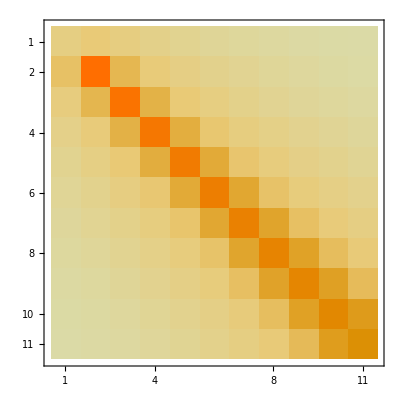

```mathematica
MatrixPlot[Matd]
```

```mathematica
Γheat = 0.1* Table[(Λrecarate[[n+1]]+ Λrecerate[[n+1]]+Λcarrier[[n+1]]+Λblue[[n+1]]  +ΛscRm[[n+1]] +ΛscRp[[n+1]] +Λresc[[n+1]]+ ΛscLat[[n+1]] +  Λdoublyred[[n+1]])α/(3 Erecoil)(2/(3 kb) *10^3)^-1,{n,0,10}] (*cheated*)
```

{70817.4,78900.3,86300.5,92874.9,98504.2,103116.,106746.,109482.,111425.,112684.,113459.}

```mathematica
Γeff[n_]:=Γscatt[[n]]
```

Rate Equation

```mathematica
Pm[t_]:= {P0[t],P1[t],P2[t],P3[t],P4[t],P5[t],P6[t],P7[t],P8[t],P9[t],P10[t]};
Pm'[t]
Pmen = {P0,P1,P2,P3,P4,P5,P6,P7,P8,P9,P10};
```

{P0'[t],P1'[t],P2'[t],P3'[t],P4'[t],P5'[t],P6'[t],P7'[t],P8'[t],P9'[t],P10'[t]}

```mathematica
Clear[Γeff, Matd, Γheat, α]
```

```mathematica
R = Table[+α(Γeff[n+1]*Matd[[n+1,nt]]+Γheat[[n+1]]*Matd[[n+1,nt+1]]), {n,0,nmax},{nt,0,nmax}] ;
For[i=2,i≤ nmax+1,i++,R[[i,i]] = R[[i,i]] -(Γeff[i]+ Γheat[[i]])]
For[i=1,i≤ nmax+1,i++,R[[i,1]] = α Γheat[[i]]*Matd[[1,i]]]
R[[0,0]] =-(Γeff[1]+ Γheat[[1]]) -  α Γheat[[1]]*Matd[[1,1]];
R //MatrixForm
```

Set::partd: Part specification R ⟦ 0, 0 ⟧ is longer than depth of object.

(35.4495 | 817.916+0. ⅈ | 75.4526+0. ⅈ | 4.03426+0. ⅈ | 0.151418+0. ⅈ | 0.00438324+0. ⅈ | 0.000104197+0. ⅈ | 2.11908×10^-6+0. ⅈ | 3.78775×10^-8+0. ⅈ | 6.06077×10^-10+0. ⅈ | 8.79588×10^-12+0. ⅈ
911.271+0. ⅈ | -80150.8+0. ⅈ | 67923.2+0. ⅈ | 6849.16+0. ⅈ | 480.83+0. ⅈ | 24.1336+0. ⅈ | 0.932815+0. ⅈ | 0.0292077+0. ⅈ | 0.000767305+0. ⅈ | 0.0000173482+0. ⅈ | 3.44093×10^-7+0. ⅈ
91.9492 | 7919.19+0. ⅈ | -148521.+0. ⅈ | 120528.+0. ⅈ | 18045.9+0. ⅈ | 1733.29+0. ⅈ | 110.881+0. ⅈ | 5.21232+0. ⅈ | 0.19223+0. ⅈ | 0.00581253+0. ⅈ | 0.000148656+0. ⅈ
5.29081+0. ⅈ | 606.941+0. ⅈ | 12479.4+0. ⅈ | -210659.+0. ⅈ | 161294.+0. ⅈ | 32032.1+0. ⅈ | 3916.34+0. ⅈ | 304.981+0. ⅈ | 16.9014+0. ⅈ | 0.717912+0. ⅈ | 0.024566+0. ⅈ
0.210616 | 32.5852+0. ⅈ | 1245.29+0. ⅈ | 17495.9+0. ⅈ | -264724.+0. ⅈ | 191246.+0. ⅈ | 47000.5+0. ⅈ | 7013.54+0. ⅈ | 646.056+0. ⅈ | 41.3328+0. ⅈ | 1.98987+0. ⅈ
0.00638236+0. ⅈ | 1.32435+0. ⅈ | 82.4039+0. ⅈ | 2114.6+0. ⅈ | 22875.+0. ⅈ | -309810.+0. ⅈ | 211280.+0. ⅈ | 61357.3+0. ⅈ | 10852.9+0. ⅈ | 1158.07+0. ⅈ | 84.1714+0. ⅈ
0.00015706 | 0.0430346+0. ⅈ | 3.97987+0. ⅈ | 165.304+0. ⅈ | 3205.1+0. ⅈ | 28380.3+0. ⅈ | -344691.+0. ⅈ | 222115.+0. ⅈ | 73702.4+0. ⅈ | 15120.3+0. ⅈ | 1838.57+0. ⅈ
3.27604×10^-6+0. ⅈ | 0.00116129+0. ⅈ | 0.149766+0. ⅈ | 9.22471+0. ⅈ | 287.619+0. ⅈ | 4487.07+0. ⅈ | 33704.3+0. ⅈ | -368814.+0. ⅈ | 224897.+0. ⅈ | 83078.3+0. ⅈ | 19413.2+0. ⅈ
5.95972×10^-8 | 0.0000267498+0. ⅈ | 0.00459219+0. ⅈ | 0.39411+0. ⅈ | 18.1808+0. ⅈ | 453.454+0. ⅈ | 5916.42+0. ⅈ | 38576.5+0. ⅈ | -383403.+0. ⅈ | 221475.+0. ⅈ | 89196.9+0. ⅈ
9.64384×10^-10+0. ⅈ | 5.36993×10^-7+0. ⅈ | 0.000118465+0. ⅈ | 0.0135303+0. ⅈ | 0.868985+0. ⅈ | 32.0006+0. ⅈ | 664.019+0. ⅈ | 7426.88+0. ⅈ | 42574.8+0. ⅈ | -392793.+0. ⅈ | 212119.+0. ⅈ
1.40922×10^-11 | 9.55853×10^-9+0. ⅈ | 2.6369×10^-6+0. ⅈ | 0.000387294+0. ⅈ | 0.033149+0. ⅈ | 1.70444+0. ⅈ | 52.5415+0. ⅈ | 946.605+0. ⅈ | 9525.78+0. ⅈ | 50232.7+0. ⅈ | -396720.+0. ⅈ)

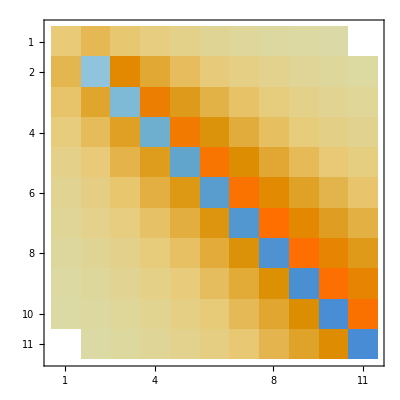

```mathematica
MatrixPlot[R]
```

```mathematica
system = Pm'[t] == R.Pm[t] ;
init=Pm[0]=={0,0,0,0,0,0,0,1,0,0,0}
```

{P0[0],P1[0],P2[0],P3[0],P4[0],P5[0],P6[0],P7[0],P8[0],P9[0],P10[0]}=={0,0,0,0,0,0,0,1,0,0,0}

{{P0→InterpolatingFunction[{{0.,4.}},<>],P1→InterpolatingFunction[{{0.,4.}},<>],P2→InterpolatingFunction[{{0.,4.}},<>],P3→InterpolatingFunction[{{0.,4.}},<>],P4→InterpolatingFunction[{{0.,4.}},<>],P5→InterpolatingFunction[{{0.,4.}},<>],P6→InterpolatingFunction[{{0.,4.}},<>],P7→InterpolatingFunction[{{0.,4.}},<>],P8→InterpolatingFunction[{{0.,4.}},<>],P9→InterpolatingFunction[{{0.,4.}},<>],P10→InterpolatingFunction[{{0.,4.}},<>]}}

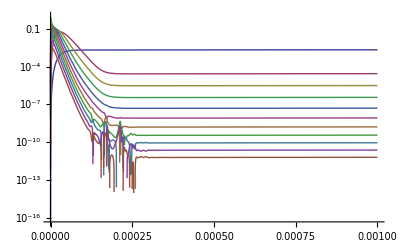

```mathematica
sol=NDSolve[LogicalExpand[Pm'[t]==R.Pm[t]&&init],Pmen,{t,0,4}]
LogPlot[Evaluate[{P0[t], P1[t],P2[t],P3[t],P4[t],P5[t],P6[t],P7[t],P8[t],P9[t],P10[t]}/.sol],{t,0,0.001}, PlotRange -> All, PlotLegend -> {0,1,2,3,4,5,6,7,8,9,10, 11}, LegendShadow -> None]
```

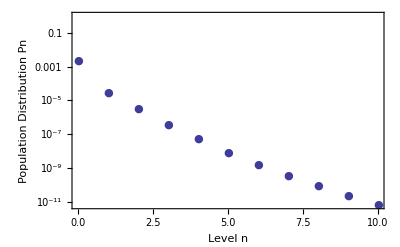

```mathematica
SteadyState = Table[
tel = 0.001;
func = Pmen[[n+1]]/.First[sol];
steadyvalue = func[tel];
{n, steadyvalue},{n,0,10}];
ListLogPlot[SteadyState, Joined -> False, PlotMarkers -> {Automatic,Small}, Frame-> True, FrameLabel-> {"Level n", "Population Distribution Pn"}]
```